```mathematica
M=0;φ=0 π/2;
u=0;v=4;
po=0;lo=5;
p=po+u*k;l=lo+v*k;
z=0zR;
L=5*10^-3;
ρ=√(x^2+y^2);
ϕ=ArcTan[x,y];
λ=1064*10^-9;
ωo=40*10^-6;
zR=(π ωo^2)/λ;
ωz=ωo*√(1+(z/zR)^2);
θG=ArcTan[zR,z];
Q=1;
k1=π/L*Q;


A=√((2 p!)/(π (p+Abs[l])!))*1/ωz*((√2*ρ)/ωz)^Abs[l]* LaguerreL[p,Abs[l],(2 ρ^2)/ωz^2]*ⅇ^(-ρ^2/ωz^2)*Exp[-ⅈ*k1*z*(1+ρ^2/(2(z^2+zR^2)))]*Exp[ⅈ*(2*p+Abs[l]+1)*θG];
Ψ1=1/2^M∑_(k=0)^M √(((M)!)/((k)! (M-k)!))*ⅇ^(ⅈ*k*φ)*ⅇ^(ⅈ*l*ϕ)*A;


W1=Ψ1;
```

```mathematica
a=√(po+Abs[lo]+2)*3.5*ωz;
In1=DensityPlot[Abs[W1]^2,{x,-a,a},{y,-a,a},PlotRange->All,PlotPoints->101,Frame->None,ColorFunction->"AvocadoColors",Exclusions->False,ImageSize->{720,720},PlotLegends->Automatic]
```

-Graphics-

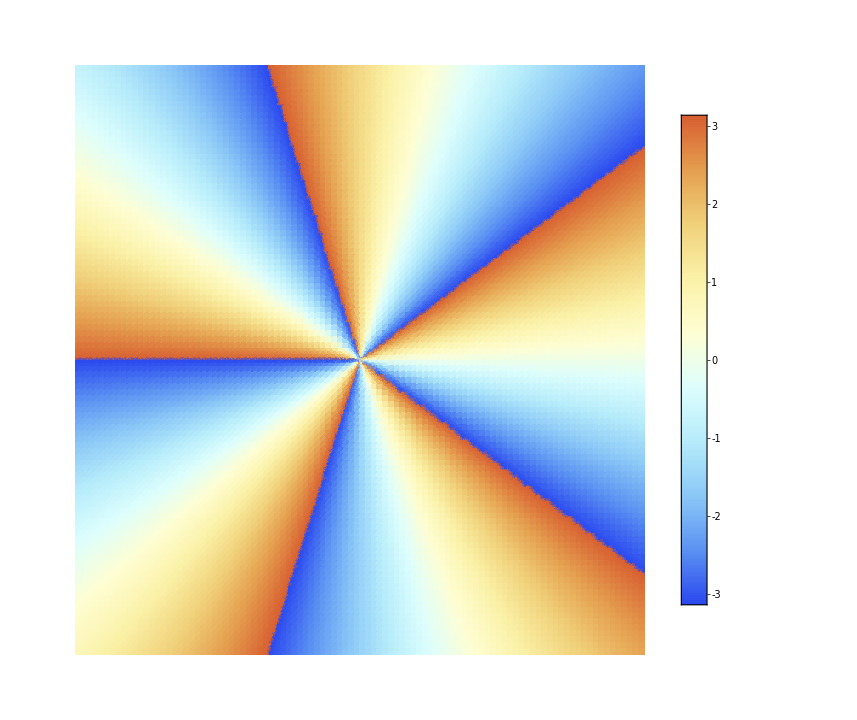

```mathematica
DensityPlot[ArcTan[Re[W1],Im[W1]],{x,-a,a},{y,-a,a},PlotRange->All,PlotPoints->101,Frame->None,ColorFunction->"LightTemperatureMap",Exclusions->False,ImageSize->{720,720},PlotLegends->Automatic]
```

```mathematica
k=750000;θ=1 π/3;θ1=2 π/2;

Ep=Exp[ⅈ (k z*Cos[θ]+(k x*Cos[θ1]+k y*Sin[θ1])*Sin[θ])];
z=0;
Int=DensityPlot[Cos[(ArcTan[Re[W1],Im[W1]]+ArcTan[Re[Ep],Im[Ep]])],{x,-a,a},{y,-a,a},PlotRange->All,PlotPoints->250,ColorFunction->GrayLevel,Frame->None,Exclusions->None,ImageSize->{1080,1080}]
```

-Graphics-

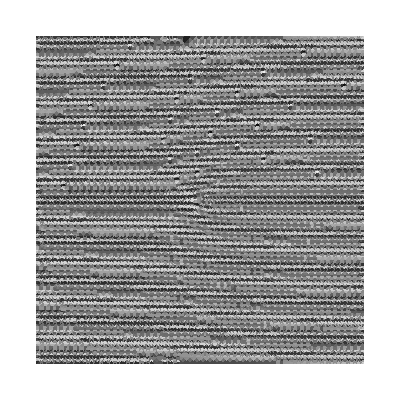

```mathematica
k=750000;θ=1 π/3;θ1=π/2;

Ep=Exp[ⅈ (k z*Cos[θ]+(k x*Cos[θ1]+k y*Sin[θ1])*Sin[θ])];
z=0;
Int=DensityPlot[Cos[(ArcTan[Re[W1],Im[W1]]+ArcTan[Re[Ep],Im[Ep]])],{x,-a,a},{y,-a,a},PlotRange->All,PlotPoints->50,ColorFunction->GrayLevel,Frame->None,Exclusions->None]
```